```mathematica
Get[ResourceFunction["NotebookRelativePath"][{"Packages", "Utils.wl"}]]
```

# Pulse Width Modulation (PWM)

## A prototype, self-teaching lesson with direct demonstrations

Egar Almeida

Flip Phillips / Daavid Väänänen

## Pre-requisites

Arduino

GPIO

digitalRead(), digitalWrite()

Electronics

Voltage, current, resistance

Ohm's law

Reading a waveform

Basic components

## Technical Explanation

## Frequency

We’ll begin the lesson by plotting a square wave

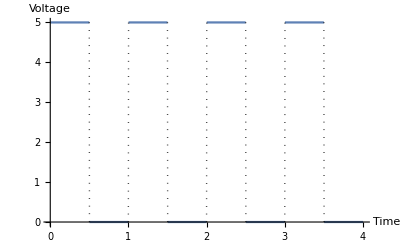

```mathematica
Plot[5 UnitStep[SquareWave[n]], {n,0,4},ExclusionsStyle-> Dotted, AxesLabel->{"Time", "Voltage"}]
```

This square wave shows an alternation between 0 and 5 volts: We see 5 volts for a duration of half a second, then 0 volts for a duration of half a second.

This wave can be read as “a square wave of 1Hz with a 50% duty cycle”.

Hz (Hertz) is the frequency of the wave. 1Hz means 1 cycle per second.

Duty cycle is the portion of time during each cycle where the wave is at 5 volts, also known as “On” time (or HIGH in Arduino). 50% means that we have 5 volts for half the time and 0 volts for half the time.

If we were to connect an LED to a microcontroller pin outputting this wave, we’d get a blinking LED. In Arduino, we could do it with:

void loop() {
	digitalWrite(LED_PIN, HIGH);		// Turn LED on
	delay(500);					// Wait for 500 mS (half a second)
	digitalWrite(LED_PIN, LOW);		// Turn LED off
	delay(500);					// Wait for 500 mS again
}

```mathematica
Animate[ledSymbolF[onOff], {onOff, 0, 1, 1}, DefaultDuration->1,]
```

What happens when we increase the frequency of this wave?
The LED would blink faster, but frequencies above 60hz would make it impossible for the human eye to distinguish the flickering due to flicker fusion and it’d seem like the LED is fully ON all the time.

Try varying the frequency of the square wave to see the waveform representation:

```mathematica
Manipulate[Column[{Style[IntegerPart[frequency] "Hz",20],Show[Plot[5 UnitStep[SquareWave[n*frequency]], {n,0,4},ExclusionsStyle->Automatic, AxesLabel->{"Time", "Voltage"}], ImageSize->Medium]}], {frequency, 1, 10, 1},]
```

## Duty Cycle

Now that we’ve seen what altering the frequency does, let’s examine what happens when we alter the duty cycle between 20% and 100%

```mathematica
Manipulate[Column[{Style[IntegerPart[dutyCycle*100/1]"%",20],Show[Plot[5squareWave[t,1,dutyCycle],{t,0,5}, ExclusionsStyle->Automatic, AxesLabel->{"Time", "Voltage"}], ImageSize->Medium]}], {dutyCycle, 0.2, 1, 0.1}]
```

By changing the duty cycle, you effectively change the time a device is in the ON state. The higher the duty cycle, the longer a device stays ON.

```mathematica
Manipulate[Column[{Style[IntegerPart[dutyCycle*100/1] "%", Large],ledSymbolF[dutyCycle]}], {dutyCycle, 0, 1., .1}]
```

As you can observe in this simulation, the LED fades.
This has an interesting effect in voltage and current : Their average value is defined by the duty cycle, which means the LED won' t be perceived as blinking, but instead it will be perceived as fading.

## Demonstrations

## Frequency